```mathematica
初值微小变化对Lorenz方程求解结果的影响
```

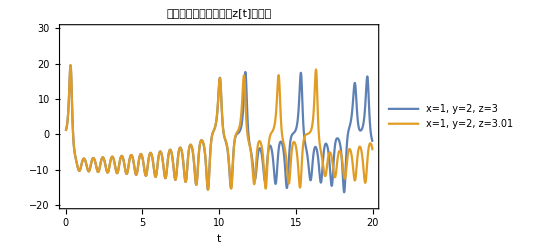

```mathematica
Clear["Global`*"]
σ=10;(*系数*)
γ=29;(*系数*)
b=8/3;(*系数*)
tt=20;(*时间*)

(*第一组初始值*)
x0 = 1;
y0=2;
z0=3.;

(*数值求解洛伦兹方程*)
f = {D[x[t],t]==σ*(y[t]-x[t]),D[y[t],t]==γ*x[t]-y[t]-x[t]*z[t],D[z[t],t]==x[t]*y[t]-b*z[t],x[0]==x0,y[0]==y0,z[0]==z0};
s1=NDSolve[f,{x,y,z},{t,0,tt},MaxSteps->Infinity];

(*第二组初始值*)
x0 = 1;
y0=2;
z0=3.01;

(*数值求解洛伦兹方程*)
f = {D[x[t],t]==σ*(y[t]-x[t]),D[y[t],t]==γ*x[t]-y[t]-x[t]*z[t],D[z[t],t]==x[t]*y[t]-b*z[t],x[0]==x0,y[0]==y0,z[0]==z0};
s2=NDSolve[f,{x,y,z},{t,0,tt},MaxSteps->Infinity];

(*画不同初始值对应的z[t]对比图*)
Plot[{Evaluate[{x[t]/.s1}],Evaluate[{x[t]/.s2}]},{t,0,tt},PlotLegends->{"x=1, y=2, z=3","x=1, y=2, z=3.01"},PlotRange->{{0,tt},{-20,30}},Frame->True,AxesLabel->{Style["t",17]},PlotLabel->"初始值对结果的影响，z[t]对比图"]
```